# Population Growth

```mathematica
(* initially, there are 100 people at age 10*)
(* age over 10 will give birth *)
```

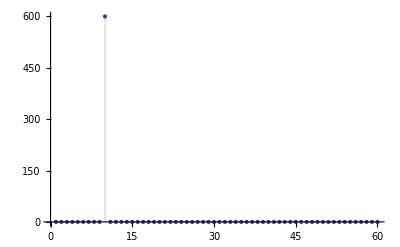

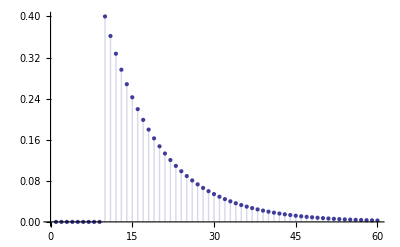

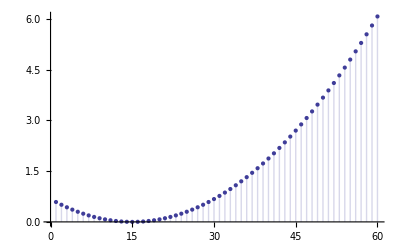

```mathematica
(* set array as age group *)
Array[age,60];
Table[age[i]=0,{i,1,60}];
age[10]=600;
Array[birth,60];
Table[birth[i] = 0,{i,1,9}];
Table[birth[i] = 0.4 Exp[-(i-10)0.1],{i,10,60}];
Array[death,60];
Table[death[i] =0.003(i-15)^2,{i,1,60}];
ListPlot[Table[age[i],{i,1,60}],Filling->Axis]
ListPlot[Table[birth[i],{i,1,60}],Filling->Axis]
ListPlot[Table[death[i],{i,1,60}],Filling->Axis]
```

4

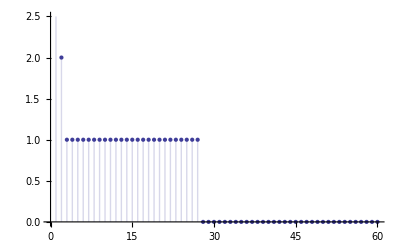

31

```mathematica
age[1]=Round[Sum[age[i]*birth[i],{i,10,60}]]
Do[
age[i]=Round[age[i-1]*(1-death[i])]
,{i,2,60}]
ListPlot[Table[age[i],{i,1,60}],Filling->Axis]
Sum[age[i],{i,1,60}]
```